# HighPT

## Flavor bounds from high-p_T tails at LHC

Keep this notebook out of git !!!

## Preamble

#### Set package directory

Make sure that the package directory is in the $Path.

```mathematica
SetDirectory@ ParentDirectory@ NotebookDirectory[];
(*AppendTo[$Path, "/path/to/HighPT"];*)
```

#### Loading the package

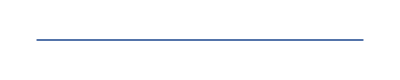

HighPT | : | High-p_T Tails
 |  | 
Authors | : | Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo,
 |  | Olcyr Sumensari, and Felix Wilsch
Reference | : | arXiv:22xx.xxxxxhttps://arxiv.org/Nonehttps://arxiv.org/HyperlinkHyperlinkActive
Website | : | https://github.com/HighPT/HighPThttps://github.com/HighPT/HighPTNonehttps://github.com/HighPT/HighPTHyperlinkHyperlinkActive

HighPT is free software under the terms of the MIT License.

Please submit bugs and feature requests using GitHub's issue system at:

https://github.com/HighPT/HighPT/issueshttps://github.com/HighPT/HighPT/issuesNonehttps://github.com/HighPT/HighPT/issuesHyperlinkHyperlinkActive

-Graphics-

Using model: SMEFT

Maximum operator mass dimension: 6

EFT series truncation at: Λ_NP^-4

```mathematica
<<HighPT`
```

#### FOR DEVELOPMENT ONLY

This allows to access all PackageScope functions in the notebook.
Remove this line eventually.

```mathematica
PrependTo[$ContextPath, "HighPT`PackageScope`"];
```

#### Load MaTeX`

```mathematica
<<MaTeX`
```

## Analysis

## Info on LHC search

```mathematica
?LHCSearch
```

### Searches

```mathematica
LHCSearch[]
```

<|tata→[arXiv:2002.12223](https://arxiv.org/abs/2002.12223),tanu→[ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/)|>

```mathematica
LHCSearch["tata"]
```

<|Info→<|PROCESS→p p > τ^- τ^+,FINALSTATE→{e[3],e[3]},EXPERIMENT→ATLAS,ARXIV→[2002.12223](https://arxiv.org/abs/2002.12223),SOURCE→https://doi.org/10.17182/hepdata.93071.v4/t3,DESCRIPTION→Observed and predicted mTtot distribution in the b-veto category of the 2tau_h channel. The last bin includes overflows.,OBSERVABLE→m_T^tot,BINS→<|OBSERVABLE→{150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500},MLL→{150,200,250,300,350,400,450,500,600,700,800,900,1000,1150,1500},PT→{0,∞}|>,LUMINOSITY→139,CMENERGY→13000|>,Observed→{1167.,1568.,1409.,1455.,1292.,650.,377.,288.,92.,57.,27.,14.,11.,13.},Expected→{1125.2,1498.3,1434.54,1495.3,1276.9,656.11,353.42,327.85,123.3,61.49,33.42,17.43,11.97,10.65},Error→{41.4616,52.2108,55.603,75.9643,93.8217,62.1782,39.6698,39.2406,18.3311,10.9369,6.7967,4.48256,3.83814,4.17861}|>

```mathematica
LHCSearch["tanu"]
```

<|Info→<|PROCESS→p p > τ ν,FINALSTATE→{e[3],ν} | {ν,e[3]},EXPERIMENT→ATLAS,ARXIV→[ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/),SOURCE→https://cds.cern.ch/record/2773301/,DESCRIPTION→Final states with a tau lepton and missing transverse momentum. The tau lepton is reconstructed in hadronic decay modes.,OBSERVABLE→m_T,BINS→<|OBSERVABLE→{200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000},MLL→{400,10000},PT→{200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}|>,LUMINOSITY→139,CMENERGY→13000|>,Observed→{2939.24,10471.3,3052.85,978.562,401.356,187.983,94.9833,53.776,21.2353,12.7264,9.94597,3.92751,0.983878,6.84837,0,0.985549},Expected→{2939.24,10274.6,2995.51,1016.39,401.356,184.452,94.9833,47.9928,26.6614,15.0947,8.228,4.93107,3.18808,3.95151,1.5,1.23738},Error→{154.045,552.37,189.112,75.7941,35.0634,20.0409,12.5365,8.43366,5.67964,4.39279,3.55724,2.27465,1.25567,2.82298,0.4,1.06915}|>

## χ^2 construction

```mathematica
?ChiSquareLHC
```

```mathematica
?MatchToSMEFT
```

### τ^- τ^+ [~40 sec]

```mathematica
χ2["ττ"]=EchoTiming@ ChiSquareLHC["tata"]
```

"σ computation: "  14.8429

"ϵ substitution: "  26.1065

EventYield::missingeff: Not all required efficincies have been given. The missing efficiencies are set to zero, these include: {Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[1],d[2]}],Efficiency[vector,{regular,ZBoson},{0,0},{Left,Left},{e[3],e[3],d[1],d[2]}],Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[1],d[3]}],«5»,Efficiency[vector,{regular,Photon},{0,0},{Left,Left},{e[3],e[3],d[3],d[1]}],Efficiency[vector,{regular,ZBoson},{0,0},{Left,Left},{e[3],e[3],d[3],d[1]}],«150»}.

43.5739

{0.000581712 (41.8-139000 (1))^2,0.000366842 (69.7-139000 (1))^2,0.000323447 (-25.54-139000 1)^2,8,0.0497677 (1)^2,0.0678826 (-0.97-139000 (1+900+1))^2,0.0572712 (2.35-139000 (1))^2}
 |  |  |  |

### τ ν [~210 sec]

```mathematica
χ2["τν"]=EchoTiming@ ChiSquareLHC["tanu"]
```

Computing observable for tanu search: [ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/)

PROCESS | : | pp → τ^-ν̄
pp → ντ^+
EXPERIMENT | : | ATLAS
ARXIV | : | [ATLAS-CONF-2021-025](https://cds.cern.ch/record/2773301/)
SOURCE | : | https://cds.cern.ch/record/2773301/
OBSERVABLE | : | m_T
BINNING m_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}
LUMINOSITY [fb^-1] | : | 139
BINNING √(ŝ) [GeV] | : | {400,10000}
BINNING p_T [GeV] | : | {200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1750,2000,10000}

Computing cross sections for finalstate: {e[3],ν}

### Match to the SMEFT and combine the χ^2

Convert standard deviations σ to confidence level CL

```mathematica
StDtoCL[n_Integer]:=N@Erf[n/(√2)]
```

```mathematica
σ1=StDtoCL[1]
σ2=StDtoCL[2]
```

0.682689

0.9545

#### Define NP scale

```mathematica
ΛNP=1000;
```

#### Sum all bins and match form factors to the SMEFT

```mathematica
χ2SMEFT["ττ"]=MatchToSMEFT[Plus@@χ2["ττ"],ΛNP];
```

```mathematica
χ2SMEFT["τν"]=MatchToSMEFT[Plus@@χ2["τν"],ΛNP];
```

For simplicity assume only real coefficients

```mathematica
MakeReal={Complex[a_,b_]:>a, Conjugate[wc_WC]:>wc};
```

```mathematica
χ2SMEFTre["ττ"]=χ2SMEFT["ττ"]/.MakeReal;
χ2SMEFTre["τν"]=χ2SMEFT["τν"]/.MakeReal;
```

#### combine

```mathematica
χ2SMEFTre["combined"]=χ2SMEFTre["ττ"]+χ2SMEFTre["τν"];
```

## PlotConfidenceIntervals

```mathematica
?ConfidenceRegion
```

```mathematica
?PlotConfidenceIntervals
```

### some example coefficients with all possible flavor combinations

```mathematica
parameters["lq1"]={
	WC["lq1",{3,3,3,3}],
	WC["lq1",{3,3,2,2}],
	WC["lq1",{3,3,1,1}],
	WC["lq1",{3,3,2,3}],
	WC["lq1",{3,3,1,3}],
	WC["lq1",{3,3,1,2}]
};
intervals["lq1"]=ConfidenceRegion[χ2SMEFTre["combined"],{#},{},σ2]&/@parameters["lq1"];
```

```mathematica
parameters["lq3"]={
	WC["lq3",{3,3,3,3}],
	WC["lq3",{3,3,2,2}],
	WC["lq3",{3,3,1,1}],
	WC["lq3",{3,3,2,3}],
	WC["lq3",{3,3,1,3}],
	WC["lq3",{3,3,1,2}]
};
intervals["lq3"]=ConfidenceRegion[χ2SMEFTre["combined"],{#},{},σ2]&/@parameters["lq3"];
```

```mathematica
parameters["lequ3"]={
	WC["lequ3",{3,3,2,2}],
	WC["lequ3",{3,3,1,1}],
	WC["lequ3",{3,3,3,2}],
	WC["lequ3",{3,3,3,1}],
	WC["lequ3",{3,3,2,1}],
	WC["lequ3",{3,3,1,2}]
};
intervals["lequ3"]=ConfidenceRegion[χ2SMEFTre["combined"],{#},{},σ2]&/@parameters["lequ3"];
```

```mathematica
parameters["ledq"]={
	WC["ledq",{3,3,3,3}],
	WC["ledq",{3,3,2,2}],
	WC["ledq",{3,3,1,1}],
	WC["ledq",{3,3,2,3}],
	WC["ledq",{3,3,1,3}],
	WC["ledq",{3,3,3,2}],
	WC["ledq",{3,3,3,1}],
	WC["ledq",{3,3,1,2}],
	WC["ledq",{3,3,2,1}]
};
intervals["ledq"]=ConfidenceRegion[χ2SMEFTre["combined"],{#},{},σ2]&/@parameters["ledq"];
```

### Plot the confidence intervals for all the parameters

```mathematica
?PlotConfidenceIntervals
```

𝒞_lq_3333^(1) : {{-0.896778,0.617962}}

𝒞_lq_3322^(1) : {{-0.269217,0.187167}}

𝒞_lq_3311^(1) : {{-0.0174474,0.0637925}}

𝒞_lq_3323^(1) : {{-0.337435,0.337435}}

𝒞_lq_3313^(1) : {{-0.167428,0.167428}}

𝒞_lq_3312^(1) : {{-0.0692284,0.0692284}}

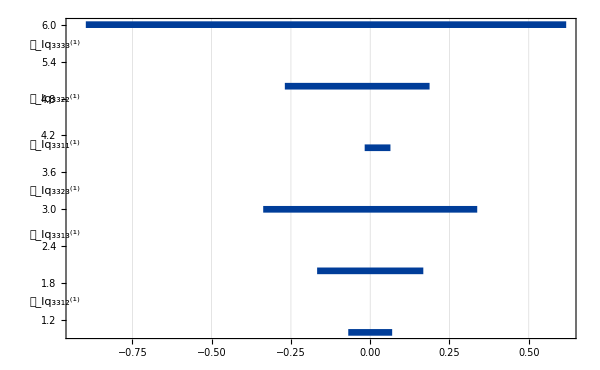

```mathematica
PlotConfidenceIntervals[intervals["lq1"]]
```

𝒞_lq_3333^(3) : {{-0.862298,0.599738}}

𝒞_lq_3322^(3) : {{-0.0626049,0.022775}}

𝒞_lq_3311^(3) : {{-0.010796,-0.0010736}}

𝒞_lq_3323^(3) : {{-0.0761477,0.0735222}}

𝒞_lq_3313^(3) : {{-0.0218046,0.02173}}

𝒞_lq_3312^(3) : {{-0.0170462,0.00370863}}

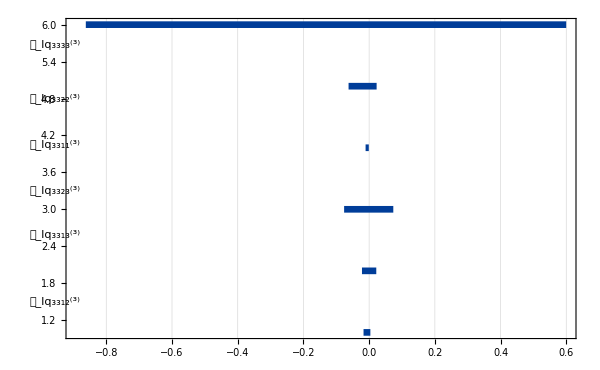

```mathematica
PlotConfidenceIntervals[intervals["lq3"]]
```

𝒞_lequ_3322^(3) : {{-0.0813943,0.0813943}}

𝒞_lequ_3311^(3) : {{-0.0101429,0.0101429}}

𝒞_lequ_3332^(3) : {{-0.157196,0.157196}}

𝒞_lequ_3331^(3) : {{-0.0251052,0.0251052}}

𝒞_lequ_3321^(3) : {{-0.0158413,0.0158413}}

𝒞_lequ_3312^(3) : {{-0.0276556,0.0276556}}

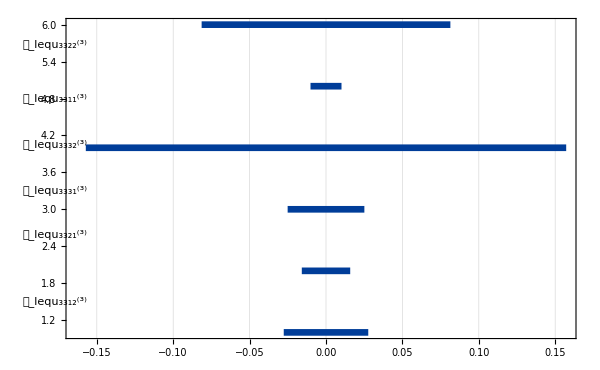

```mathematica
PlotConfidenceIntervals[intervals["lequ3"]]
```

𝒞_ledq_3333 : {{-0.607781,0.607781}}

𝒞_ledq_3322 : {{-0.083898,0.083898}}

𝒞_ledq_3311 : {{-0.0174458,0.0174458}}

𝒞_ledq_3323 : {{-0.364843,0.364843}}

𝒞_ledq_3313 : {{-0.180231,0.180231}}

𝒞_ledq_3332 : {{-0.134729,0.134729}}

𝒞_ledq_3331 : {{-0.0406975,0.0406975}}

𝒞_ledq_3312 : {{-0.0402151,0.0402151}}

𝒞_ledq_3321 : {{-0.0266072,0.0266072}}

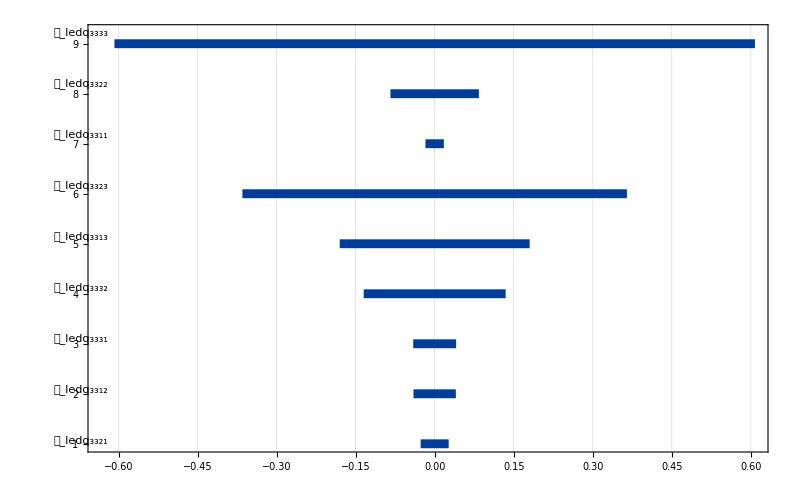

```mathematica
PlotConfidenceIntervals[intervals["ledq"],ImageSize->800]
```

## 2D parameter fit

```mathematica
?ConfidenceRegion
```

```mathematica
?PlotConfidenceRegion
```

### 1) (C^(1))_(lq,3323)=(C^(3))_(lq,3323) and (C^(1))_(lq,3333)=(C^(3))_(lq,3333)

#### Define parameters for confidence region

```mathematica
(* minimize with respect to these parameters *)
parameters1={ 
	WC["lq1",{3,3,2,3}],
	WC["lq1",{3,3,3,3}]
};

(* relations for the minimization *)
relations1={ 
	WC["lq3",{3,3,3,3}]->WC["lq1",{3,3,3,3}],
	WC["lq3",{3,3,2,3}]->WC["lq1",{3,3,2,3}]
};
```

#### Derive confidence regions for 1σ and 2σ

NC

```mathematica
Region1["1σ"]["ττ"]=ConfidenceRegion[χ2SMEFTre["ττ"],parameters1,relations1,σ1 ];
Region1["2σ"]["ττ"]=ConfidenceRegion[χ2SMEFTre["ττ"],parameters1,relations1,σ2 ];
```

CC

```mathematica
Region1["1σ"]["τν"]=ConfidenceRegion[χ2SMEFTre["τν"],parameters1,relations1,σ1 ];
Region1["2σ"]["τν"]=ConfidenceRegion[χ2SMEFTre["τν"],parameters1,relations1,σ2 ];
```

combined

```mathematica
Region1["1σ"]["comb"]=ConfidenceRegion[χ2SMEFTre["combined"],parameters1,relations1,σ1 ];
Region1["2σ"]["comb"]=ConfidenceRegion[χ2SMEFTre["combined"],parameters1,relations1,σ2 ];
```

#### Plot

```mathematica
(* https://mathematica.stackexchange.com/questions/206173/increasing-the-length-of-frame-ticks *)
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.018,.01}][##]&;
```

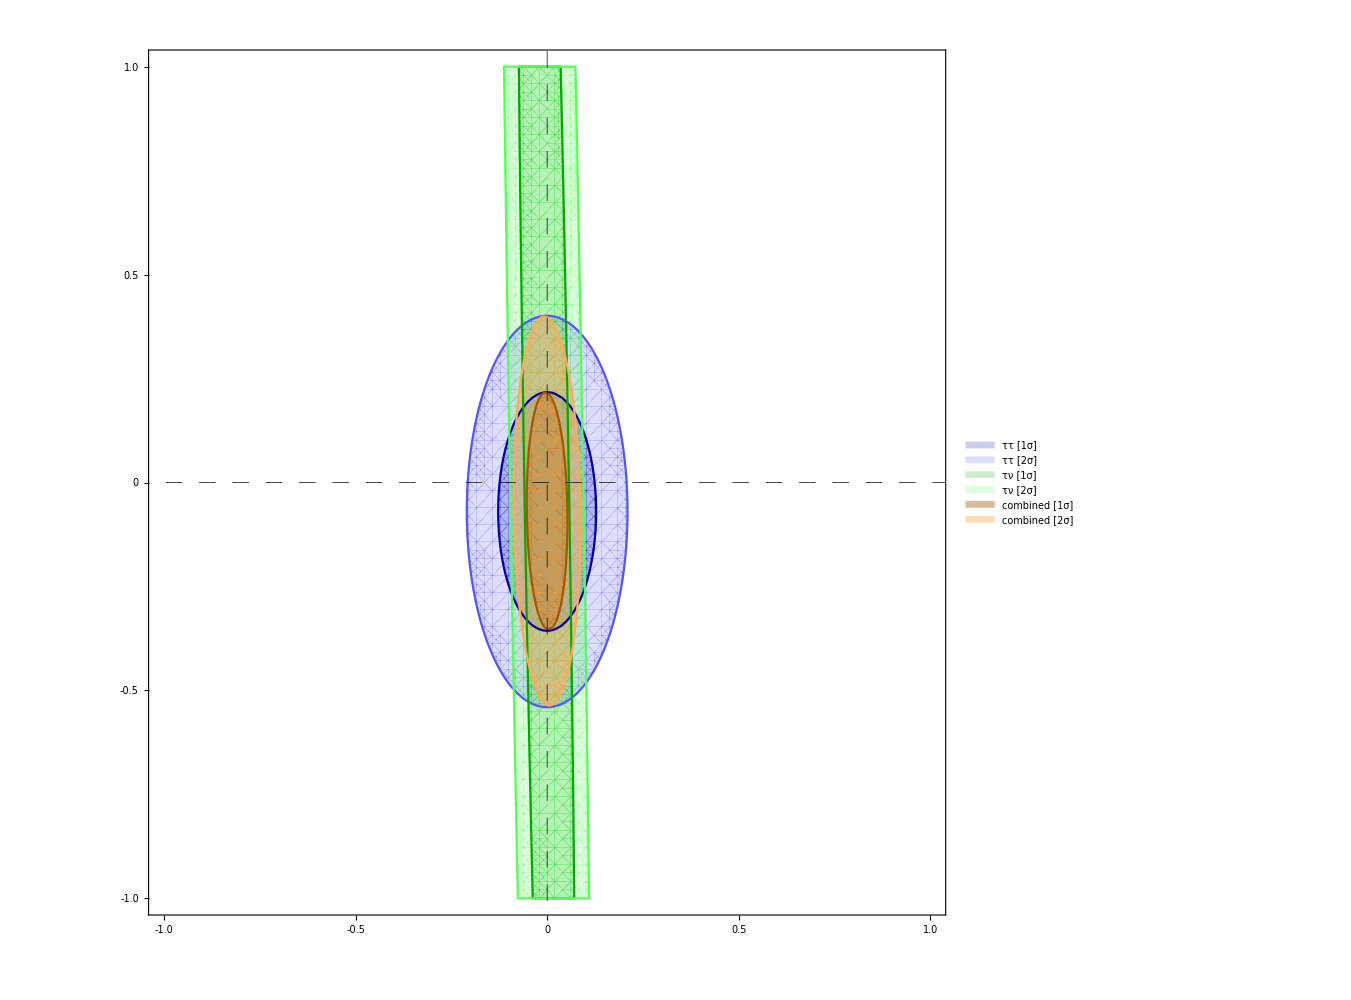

```mathematica
plt1=PlotConfidenceRegion[
	{
		Region1["1σ"]["ττ"],Region1["2σ"]["ττ"],
		Region1["1σ"]["τν"],Region1["2σ"]["τν"],
		Region1["1σ"]["comb"],Region1["2σ"]["comb"]
	},
	{-1,+1},{-1,+1}
	,
	(* Options *)
	PlotStyle->{
		Directive[Darker@Blue, Opacity[0.2]],Directive[Lighter@Blue, Opacity[0.2]],
		Directive[Darker@Green, Opacity[0.2]],Directive[Lighter@Green, Opacity[0.2]],
		Directive[Darker@Orange, Opacity[0.4]],Directive[Lighter@Orange, Opacity[0.4]]
	},
	BoundaryStyle->{
		1->Directive[Darker@Blue],2->Directive[Lighter@Blue],
		3->Directive[Darker@Green],4->Directive[Lighter@Green],
		5->Directive[Darker@Orange],6->Directive[Lighter@Orange]
	},
	PlotLegends->Placed[
		SwatchLegend[
			Automatic,
			{
				"ττ [1σ]","ττ [2σ]",
				"τν [1σ]","τν [2σ]",
				"combined [1σ]", "combined [2σ]"
			},
			LegendFunction->(Framed[#,Background->White,ImageMargins->14,RoundingRadius->4,FrameStyle->Gray]&),
			LabelStyle->{FontSize->28,FontFamily->"Times"}
		],
		{Right,Top}
	],
	FrameLabel->{
		MaTeX["C_{\\underset{3323}{lq}}^{(1)} = C_{\\underset{3323}{lq}}^{(3)}",FontSize->36],
		MaTeX["C_{\\underset{3333}{lq}}^{(1)} = C_{\\underset{3333}{lq}}^{(3)}",FontSize->36]
	}
];
Magnify[%,0.5]
```

### 2) (C^(1))_(lequ,3332)=-1/4(C^(3))_(lequ,3332) and (C^(1))_(lequ,3333)=-1/4(C^(3))_(lequ,3333)

#### Define parameters for confidence region

```mathematica
(* minimize with respect to these parameters *)
parameters2={ 
	WC["lequ1",{3,3,3,2}],
	WC["lequ1",{3,3,3,3}]
};

(* relations for the minimization *)
relations2={ 
	WC["lequ3",{3,3,3,3}]->-1/4*WC["lequ1",{3,3,3,3}],
	WC["lequ3",{3,3,2,3}]->-1/4*WC["lequ1",{3,3,2,3}]
};
```

#### Derive confidence regions for 1σ and 2σ

NC [no contrition]

```mathematica
(*
Region2["1σ"]["ττ"]=ConfidenceRegion[χ2SMEFTre["ττ"],parameters2,relations2,σ1 ];
Region2["2σ"]["ττ"]=ConfidenceRegion[χ2SMEFTre["ττ"],parameters2,relations2,σ2 ];
*)
```

CC

```mathematica
Region2["1σ"]["τν"]=ConfidenceRegion[χ2SMEFTre["τν"],parameters2,relations2,σ1 ];
Region2["2σ"]["τν"]=ConfidenceRegion[χ2SMEFTre["τν"],parameters2,relations2,σ2 ];
```

Warning: The given χ^2 does not depend on the specified parameter: WC[lequ1,{3,3,3,3}]

Warning: The given χ^2 does not depend on the specified parameter: WC[lequ1,{3,3,3,3}]

#### Plot

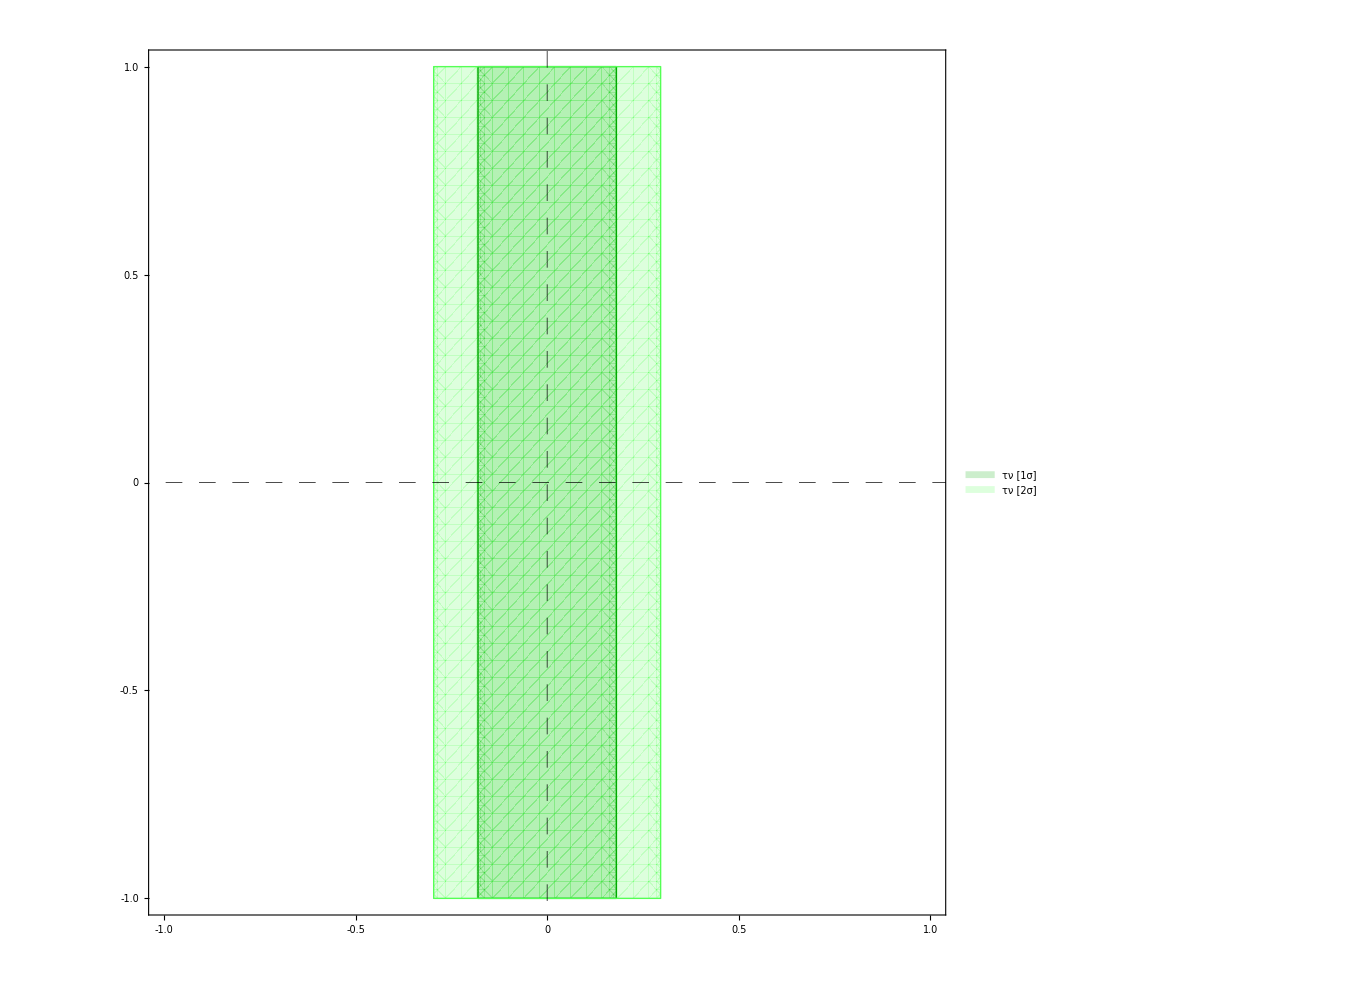

```mathematica
plt2=PlotConfidenceRegion[
	{
		Region2["1σ"]["τν"],Region2["2σ"]["τν"]
	},
	{-1,+1},{-1,+1}
	,
	(* Options *)
	PlotStyle->{
		Directive[Darker@Green, Opacity[0.2]],Directive[Lighter@Green, Opacity[0.2]]
	},
	BoundaryStyle->{
		1->Directive[Darker@Green,Thin],2->Directive[Lighter@Green,Thin]
	},
	PlotLegends->Placed[SwatchLegend[
		Automatic,
		{
			"τν [1σ]","τν [2σ]"
		},
		LegendFunction->(Framed[#,Background->White]&)
	],{0.87,0.1}],
	FrameLabel->{
		MaTeX["C_{\\underset{3323}{lequ}}^{(1)} = -\\frac{1}{4} C_{\\underset{3323}{lequ}}^{(3)}"],
		MaTeX["C_{\\underset{3333}{lequ}}^{(1)} = -\\frac{1}{4} C_{\\underset{3333}{lequ}}^{(3)}"]
	},
	PlotPoints->50,
	ImageSize->{1000,1000}
];
Magnify[%,0.5]
```

### 3) (C^(1))_(lequ,3332)=+1/4(C^(3))_(lequ,3332) and (C^(1))_(lequ,3333)=+1/4(C^(3))_(lequ,3333)

#### Define parameters for confidence region

```mathematica
(* minimize with respect to these parameters *)
parameters3={ 
	WC["lequ1",{3,3,3,2}],
	WC["lequ1",{3,3,3,3}]
};

(* relations for the minimization *)
relations3={ 
	WC["lequ3",{3,3,3,3}]->+1/4*WC["lequ1",{3,3,3,3}],
	WC["lequ3",{3,3,2,3}]->+1/4*WC["lequ1",{3,3,2,3}]
};
```

#### Derive confidence regions for 1σ and 2σ

NC [no contrition]

```mathematica
(*
Region3["1σ"]["ττ"]=ConfidenceRegion[χ2SMEFTre["ττ"],parameters3,relations3,σ1 ];
Region3["2σ"]["ττ"]=ConfidenceRegion[χ2SMEFTre["ττ"],parameters3,relations3,σ2 ];
*)
```

CC

```mathematica
Region3["1σ"]["τν"]=ConfidenceRegion[χ2SMEFTre["τν"],parameters3,relations3,σ1 ];
Region3["2σ"]["τν"]=ConfidenceRegion[χ2SMEFTre["τν"],parameters3,relations3,σ2 ];
```

Warning: The given χ^2 does not depend on the specified parameter: WC[lequ1,{3,3,3,3}]

Warning: The given χ^2 does not depend on the specified parameter: WC[lequ1,{3,3,3,3}]

#### Plot

```mathematica
plt3=PlotConfidenceRegion[
	{
		Region3["1σ"]["τν"],Region3["2σ"]["τν"]
	},
	{-1,+1},{-1,+1}
	,
	(* Options *)
	PlotStyle->{
		Directive[Darker@Green, Opacity[0.2]],Directive[Lighter@Green, Opacity[0.2]]
	},
	BoundaryStyle->{
		1->Directive[Darker@Green,Thin],2->Directive[Lighter@Green,Thin]
	},
	PlotLegends->Placed[SwatchLegend[
		Automatic,
		{
			"τν [1σ]","τν [2σ]"
		},
		LegendFunction->(Framed[#,Background->White]&)
	],{0.87,0.1}],
	FrameLabel->{
		MaTeX["C_{\\underset{3323}{lequ}}^{(1)} = +\\frac{1}{4} C_{\\underset{3323}{lequ}}^{(3)}"],
		MaTeX["C_{\\underset{3333}{lequ}}^{(1)} = +\\frac{1}{4} C_{\\underset{3333}{lequ}}^{(3)}"]
	},
	PlotPoints->50,
	ImageSize->{1000,1000}
];
Magnify[%,0.5]
```

-Graphics-

### Export figures

```mathematica
(*Export["ConfidenceRegion1.jpeg",plt1]*)
Export["ConfidenceRegion1.pdf",Rasterize[plt1,RasterSize->5000,ImageResolution->1000,ImageSize->800]]
```

ConfidenceRegion1.pdf

```mathematica
(*Export["ConfidenceRegion2.jpeg",plt2]*)
Export["ConfidenceRegion2.pdf",Rasterize[plt2,RasterSize->5000,ImageResolution->1000, ImageSize->800]]
```

ConfidenceRegion2.pdf

```mathematica
(*Export["ConfidenceRegion3.jpeg",plt3]*)
Export["ConfidenceRegion3.pdf",Rasterize[plt3,RasterSize->5000,ImageResolution->1000,ImageSize->800]]
```

ConfidenceRegion3.pdf